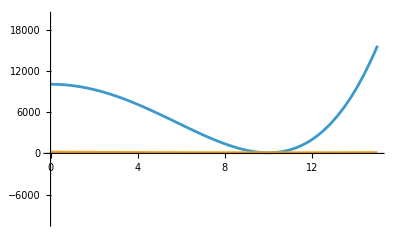

```mathematica
Plot[{(p^2-p0^2)^2+m2/.{p0->10,m2->100},(p-p0)^2+m2/.{p0->10,m2->100}},{p,0,15},PlotRange->{All,{-10000,20000}}]
```

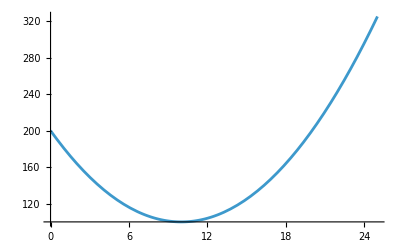

```mathematica
Plot[{(p-p0)^2+m2/.{p0->10,m2->100}},{p,0,25},PlotRange->{All,All}]
```

```mathematica
p/(2 π^2) Sin[p r]/r
```

```mathematica
1/((p^2-p0^2)^2+m2)
```

1/(m2+(p^2-p0^2)^2)

```mathematica
Solve[Z(p^2-p0^2)^2+m^2==0,p]
```

{{p→-√(p0^2-(ⅈ m)/(√Z))},{p→√(p0^2-(ⅈ m)/(√Z))},{p→-√(p0^2+(ⅈ m)/(√Z))},{p→√(p0^2+(ⅈ m)/(√Z))}}

```mathematica
2π ⅈ (Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/(Z(p^2-p0^2)^2+m^2),{p,-√(p0^2-(ⅈ m)/(√Z))}]+Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/(Z(p^2-p0^2)^2+m^2),{p,√(p0^2-(ⅈ m)/(√Z))}]+Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/(Z(p^2-p0^2)^2+m^2),{p,-√(p0^2+(ⅈ m)/(√Z))}]+Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/(Z(p^2-p0^2)^2+m^2),{p,√(p0^2+(ⅈ m)/(√Z))}])//Simplify
```

(ⅈ (ⅇ^(-ⅈ r √(p0^2-(ⅈ m)/(√Z)))+ⅇ^(ⅈ r √(p0^2-(ⅈ m)/(√Z)))-ⅇ^(-ⅈ r √(p0^2+(ⅈ m)/(√Z)))-ⅇ^(ⅈ r √(p0^2+(ⅈ m)/(√Z)))))/(8 m π r √Z)

```mathematica
Series[ⅇ^(-ⅈ r √(p0^2-(ⅈ m)/(√Z))),{p0,0,3}]
```

ⅇ^(-ⅈ r √(-(ⅈ m)/(√Z)))-(ⅈ ⅇ^(-ⅈ r √(-(ⅈ m)/(√Z))) r p0^2)/(2 √(-(ⅈ m)/(√Z)))+O[p0]^4

```mathematica
Solve[(p^4-2 p^2 p0^2)+m^2==0,p]
```

{{p→-√(p0^2-√(-m^2+p0^4))},{p→√(p0^2-√(-m^2+p0^4))},{p→-√(p0^2+√(-m^2+p0^4))},{p→√(p0^2+√(-m^2+p0^4))}}

```mathematica
Simplify[2π ⅈ (Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/((p^4-2 p^2 p0^2)+m^2),{p,-√(p0^2-√(-m^2+p0^4))}]+Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/((p^4-2 p^2 p0^2)+m^2),{p,√(p0^2-√(-m^2+p0^4))}]+Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/((p^4-2 p^2 p0^2)+m^2),{p,-√(p0^2+√(-m^2+p0^4))}]+Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/((p^4-2 p^2 p0^2)+m^2),{p,√(p0^2+√(-m^2+p0^4))}]),Assumptions->{Z>0&&m>p0>0}]
```

-(ⅇ^(-ⅈ √(p0^2-√(-m^2+p0^4)) r)+ⅇ^(ⅈ √(p0^2-√(-m^2+p0^4)) r)-ⅇ^(-ⅈ √(p0^2+√(-m^2+p0^4)) r)-ⅇ^(ⅈ √(p0^2+√(-m^2+p0^4)) r))/(8 √(-m^2+p0^4) π r)

```mathematica
ExpToTrig[-(ⅇ^(-ⅈ √(p0^2-√(-m^2+p0^4)) r)+ⅇ^(ⅈ √(p0^2-√(-m^2+p0^4)) r)-ⅇ^(-ⅈ √(p0^2+√(-m^2+p0^4)) r)-ⅇ^(ⅈ √(p0^2+√(-m^2+p0^4)) r))/(8 √(-m^2+p0^4) π r)/.{√(-m^2+p0^4)->ⅈ A}]
```

-Cos[√(-ⅈ A+p0^2) r]/(4 √(-m^2+p0^4) π r)+Cos[√(ⅈ A+p0^2) r]/(4 √(-m^2+p0^4) π r)

```mathematica
Solve[Z(p-p0)^2+m^2==0,p]
```

{{p→(-ⅈ m+p0 √Z)/(√Z)},{p→(ⅈ m+p0 √Z)/(√Z)}}

```mathematica
Collect[2π ⅈ(Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/(Z(p-p0)^2+m^2),{p,(-ⅈ m+p0 √Z)/(√Z)}]+Residue[(-ⅈ p)/(4 π^2) ⅇ^(ⅈ p r)/r 1/(Z(p-p0)^2+m^2),{p,(ⅈ m+p0 √Z)/(√Z)}]),ⅇ^(ⅈ p0 r)]
```

2 ⅈ ⅇ^(ⅈ p0 r) π (-(ⅈ ⅇ^(-(m r)/(√Z)))/(8 π^2 r Z)-(ⅈ ⅇ^((m r)/(√Z)))/(8 π^2 r Z)-(ⅇ^(-(m r)/(√Z)) p0)/(8 m π^2 r √Z)+(ⅇ^((m r)/(√Z)) p0)/(8 m π^2 r √Z))

```mathematica
h^2/(2π r)ⅇ^(ⅈ p0 r) (-(ⅈ ⅇ^(-(m r)/(√Z)))/(8 π^2 r Z)-(ⅈ ⅇ^((m r)/(√Z)))/(8 π^2 r Z)-(ⅇ^(-(m r)/(√Z)) p0)/(8 m π^2 r √Z)+(ⅇ^((m r)/(√Z)) p0)/(8 m π^2 r √Z))
```

```mathematica
ExpToTrig[ ⅇ^(ⅈ p0 r) ]
```

Cos[p0 r]+ⅈ Sin[p0 r]

```mathematica
Collect[h^2/(2π r)(Cos[p0 r]+ⅈ Sin[p0 r]) (-(ⅈ ⅇ^(-(m r)/(√Z)))/(8 π^2 r Z)-(ⅈ ⅇ^((m r)/(√Z)))/(8 π^2 r Z)-(ⅇ^(-(m r)/(√Z)) p0)/(8 m π^2 r √Z)+(ⅇ^((m r)/(√Z)) p0)/(8 m π^2 r √Z))//Expand,{Cos[p0 r],Sin[p0 r]}]
```

(-(ⅈ ⅇ^(-(m r)/(√Z)) h^2)/(16 π^3 r^2 Z)-(ⅈ ⅇ^((m r)/(√Z)) h^2)/(16 π^3 r^2 Z)-(ⅇ^(-(m r)/(√Z)) h^2 p0)/(16 m π^3 r^2 √Z)+(ⅇ^((m r)/(√Z)) h^2 p0)/(16 m π^3 r^2 √Z)) Cos[p0 r]+((ⅇ^(-(m r)/(√Z)) h^2)/(16 π^3 r^2 Z)+(ⅇ^((m r)/(√Z)) h^2)/(16 π^3 r^2 Z)-(ⅈ ⅇ^(-(m r)/(√Z)) h^2 p0)/(16 m π^3 r^2 √Z)+(ⅈ ⅇ^((m r)/(√Z)) h^2 p0)/(16 m π^3 r^2 √Z)) Sin[p0 r]